```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

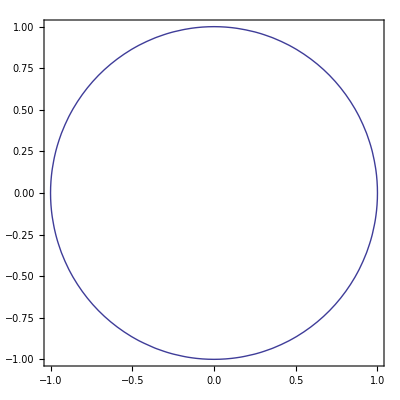

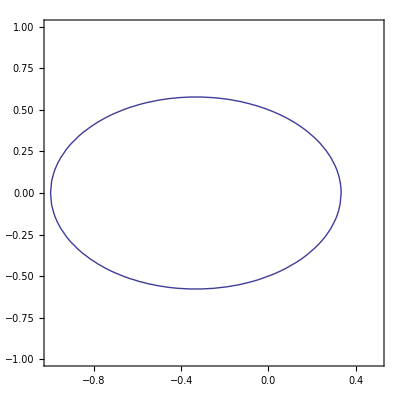

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

```mathematica
ContourPlot[(√(x^2+y^2))/(√((1-x)^2))==1/2,{x,-1,0.5},{y,-1,1}]
```

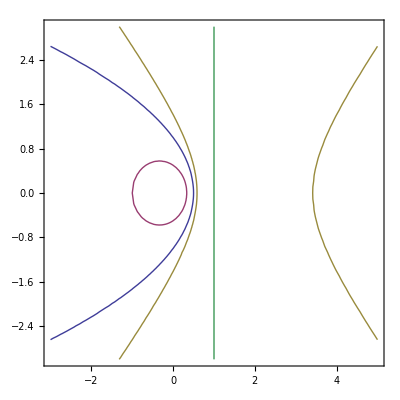

```mathematica
ContourPlot[{(√(x^2+y^2))/(√((1-x)^2))==1,(√(x^2+y^2))/(√((1-x)^2))==1/2,(√(x^2+y^2))/(√((1-x)^2))==√2,x==1},{x,-3,5},{y,-3,3}]
```

```mathematica
eq=x==x^2
sol=Solve[eq,x]
```

x==x^2

{{x→0},{x→1}}

Get::noopen: Cannot open "Graphics".

```mathematica
$Failed'
```

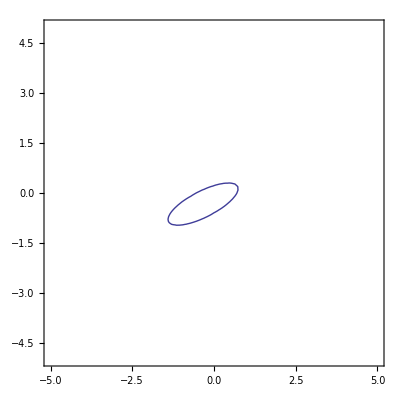

```mathematica
ContourPlot[13 x^2-32x*y+37 y^2-2x+14y-5==0,{x,-5,+5},{y,-5,+5}]
```

```mathematica
A=13 x^2-32x*y+37 y^2-2x+14y-5
u[t_]:={Cos[t],Sin[t]}
v[t_]:={-Sin[t],Cos[t]}
S={sol=Solve[{x,y}==x1*u[t]+y1*v[t],{x,y}]}
```

-5-2 x+13 x^2+14 y-32 x y+37 y^2

{{{x→x1 Cos[t]-y1 Sin[t],y→y1 Cos[t]+x1 Sin[t]}}}

```mathematica
B=A/.S
```

{{-5+14 (y1 Cos[t]+x1 Sin[t])+37 (y1 Cos[t]+x1 Sin[t])^2-2 (x1 Cos[t]-y1 Sin[t])-32 (y1 Cos[t]+x1 Sin[t]) (x1 Cos[t]-y1 Sin[t])+13 (x1 Cos[t]-y1 Sin[t])^2}}

```mathematica
B=Collect[Expand[A/.S],x1*y1]
```

{{-5-2 x1 Cos[t]+14 y1 Cos[t]+13 x1^2 Cos[t]^2+37 y1^2 Cos[t]^2+14 x1 Sin[t]+2 y1 Sin[t]-32 x1^2 Cos[t] Sin[t]+32 y1^2 Cos[t] Sin[t]+37 x1^2 Sin[t]^2+13 y1^2 Sin[t]^2+x1 y1 (-32 Cos[t]^2+48 Cos[t] Sin[t]+32 Sin[t]^2)}}

```mathematica
sol=Solve[Coefficient[B,x1*y1]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-ArcCos[-2/(√5)]},{t→ArcCos[-1/(√5)]},{t→-ArcCos[1/(√5)]},{t→ArcCos[2/(√5)]}}

```mathematica
R={t->ArcCos[2/(√5)]}
B/.R
```

{t→ArcCos[2/(√5)]}

{{-5+2 √5 x1+5 x1^2+6 √5 y1+45 y1^2}}

```mathematica
G={x1->xp-α,y1-> yp-β}
F=Expand[B/.R/.G]
```

{x1→xp-α,y1→yp-β}

{{-5+2 √5 xp+5 xp^2+6 √5 yp+45 yp^2-2 √5 α-10 xp α+5 α^2-6 √5 β-90 yp β+45 β^2}}

```mathematica
sol=Solve[Coefficient[F,xp*yp]==0,α]
```

{{}}

Solve::naqs: {-5 + y1\ (14\ Cos[t] + 2\ Sin[t]) + y1^2\ (37\ Cos[« 1 »]^2 + 32\ Cos[t]\ Sin[t] + 13\ Sin[« 1 »]^2) + x1^2\ (13\ Cos[« 1 »]^2 - 32\ Cos[t]\ Sin[t] + 37\ Sin[« 1 »]^2) + x1\ (-2\ Cos[t] + 14\ Sin[t] + y1\ (Times[« 2 »] + Times[« 3 »] + Times[« 2 »])) == 0} is not a quantified system of equations and inequalities.